```mathematica
k[d_,i_]:=1/d(1+I)+(√2)/d Exp[2π I(7/8+i/d)]
T3={k[3,0],k[3,-1],k[3,1],
k[3,0],k[3,1],k[3,-1]};
T4={k[4,0],k[4,-1],k[4,2],k[4,1],
k[4,0],k[4,2],k[4,0],k[4,2],
k[4,0],k[4,1],k[4,2],k[4,-1]};
T5={k[5,0],k[5,-1],k[5,-2],k[5,2],k[5,1],
k[5,0],k[5,-2],k[5,1],k[5,-1],k[5,2],
k[5,0],k[5,2],k[5,-1],k[5,1],k[5,-2],
k[5,0],k[5,1],k[5,2],k[5,-2],k[5,-1]};
T6={k[6,0],k[6,-1],k[6,-2],k[6,3],k[6,2],k[6,1],
k[6,0],k[6,-2],k[6,2],k[6,0],k[6,-2],k[6,2],
k[6,0],k[6,3],k[6,0],k[6,3],k[6,0],k[6,3],
k[6,0],k[6,2],k[6,-2],k[6,0],k[6,2],k[6,-2],
k[6,0],k[6,1],k[6,2],k[6,3],k[6,-2],k[6,-1]};
T7={k[7,0],k[7,-1],k[7,-2],k[7,-3],k[7,3],k[7,2],k[7,1],
k[7,0],k[7,-2],k[7,3],k[7,1],k[7,-1],k[7,-3],k[7,2],
k[7,0],k[7,-3],k[7,1],k[7,-2],k[7,2],k[7,-1],k[7,3],k[7,0],k[7,3],k[7,-1],k[7,2],k[7,-2],k[7,1],k[7,-3],
k[7,0],k[7,2],k[7,-3],k[7,-1],k[7,1],k[7,3],k[7,-2],
k[7,0],k[7,1],k[7,2],k[7,3],k[7,-3],k[7,-2],k[7,-1]};
T8={k[8,0],k[8,-1],k[8,-2],k[8,-3],k[8,4],k[8,3],k[8,2],k[8,1],
k[8,0],k[8,-2],k[8,4],k[8,2],k[8,0],k[8,-2],k[8,4],k[8,2],
k[8,0],k[8,-3],k[8,2],k[8,-1],k[8,4],k[8,1],k[8,-2],k[8,3],
k[8,0],k[8,4],k[8,0],k[8,4],k[8,0],k[8,4],k[8,0],k[8,4],
k[8,0],k[8,3],k[8,-2],k[8,1],k[8,4],k[8,-1],k[8,2],k[8,-3],
k[8,0],k[8,2],k[8,4],k[8,-2],k[8,0],k[8,2],k[8,4],k[8,-2],
k[8,0],k[8,1],k[8,2],k[8,3],k[8,4],k[8,-3],k[8,-2],k[8,-1]};
complexSplit=Function[z,{Re@z,Im@z},Listable];
ComplexPlot[list_,d_]:=ListPlot[
complexSplit@list,
AxesOrigin->{0,0},
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
ImagePadding->40,
AspectRatio->1,
Frame->True,
FrameLabel->{{Im,None},{Re,"complex plane"}},
PlotStyle->(Directive[#,PointSize[.02]]&/@{Purple,Darker@Green,Orange,Cyan,Magenta,Blue,Red}),
Epilog->{Circle[{0,0},1],
Circle[{1/#,1/#},Sqrt[2]/#]&/@Table[i,{i,2,d}]}]
```

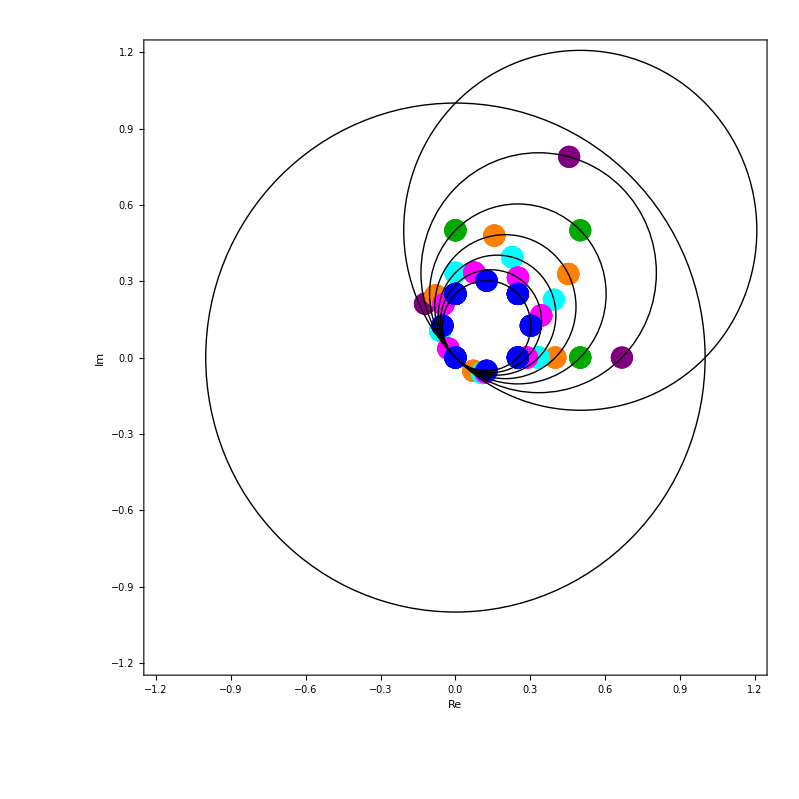

```mathematica
ComplexPlot[{T3,T4,T5,T6,T7,T8},8]
```

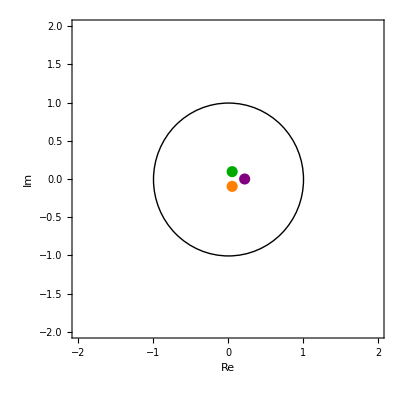

```mathematica
ComplexPlot[{{2/9},{1/9 (-1)^(1/3)},{1/18 (1-I Sqrt[3])}},0]
```

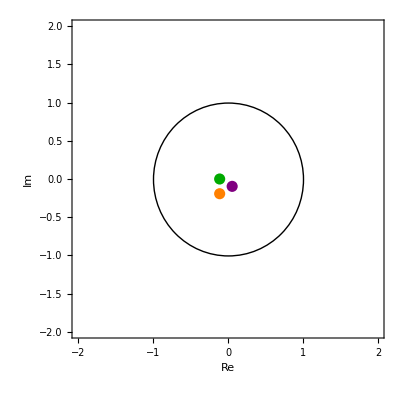

```mathematica
ComplexPlot[{{-(1/9) (-1)^(2/3)},{-(1/9)},{-(2/9) (-1)^(1/3)}},0]
```

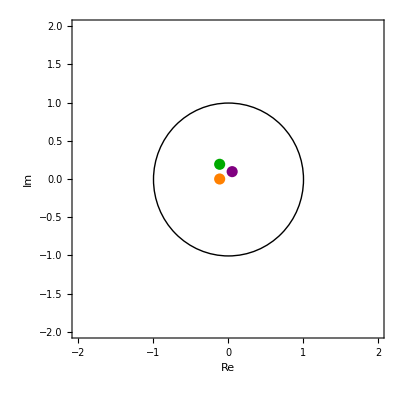

```mathematica
ComplexPlot[{{1/18 (1+I Sqrt[3])},{1/9 I (I+Sqrt[3])},{-(1/9)}},0]
```

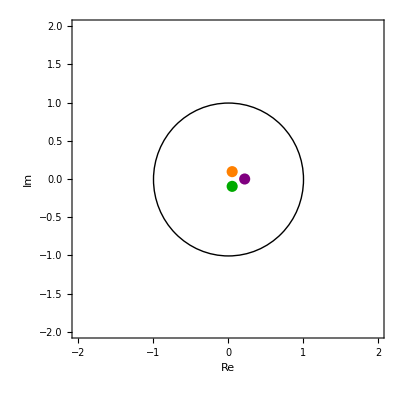

```mathematica
ComplexPlot[{{2/9},{1/18 (1-I Sqrt[3])},{1/9 (1+(-1)^(2/3))}},0]
```

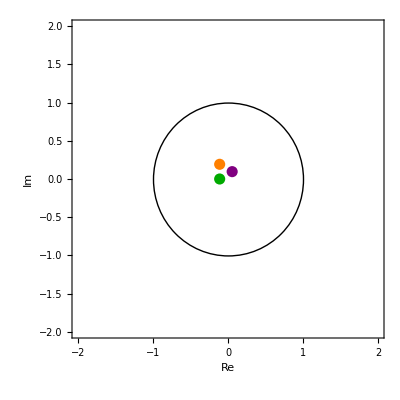

```mathematica
ComplexPlot[{{1/9 (-1)^(1/3)},{-(1/9)},{2/9 (-1)^(2/3)}},0]
```

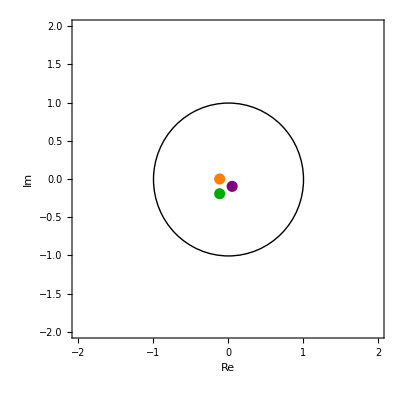

```mathematica
ComplexPlot[{{-(1/9) (-1)^(2/3)},{-(1/9) I (-I+Sqrt[3])},{-(1/9)}},0]
```

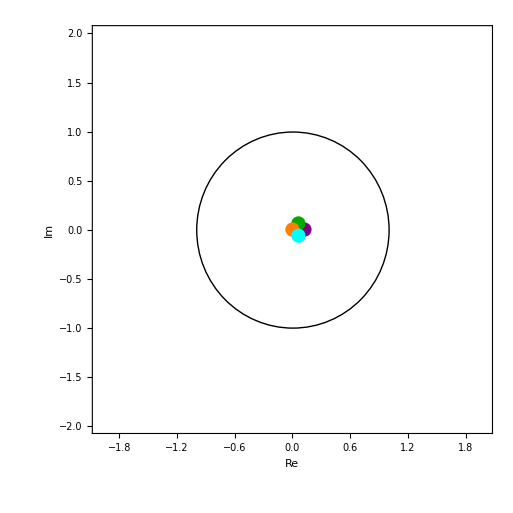

```mathematica
ComplexPlot[{{1/8},{1/16+I/16},{0},{1/16-I/16}},0]
```

```mathematica
Row[{ComplexPlot[{2/9,(2 I)/(9 I+9 Sqrt[3]),1/18 (1-I Sqrt[3]),(2 I)/(9 I-9 Sqrt[3]),-(1/9),-(4/(9-9 I Sqrt[3])),1/18 (1+I Sqrt[3]),(2 (3 I+Sqrt[3]))/(9 (-3 I+Sqrt[3])),-(1/9)},0],ComplexPlot[{1/8,1/16+I/16,0,1/16-I/16,1/16-I/16,0,-(1/16)-I/16,-(I/8),0,-(1/16)+I/16,-(1/8),-(1/16)-I/16,1/16+I/16,I/8,-(1/16)+I/16,0},0]}]
```

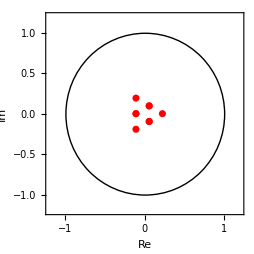
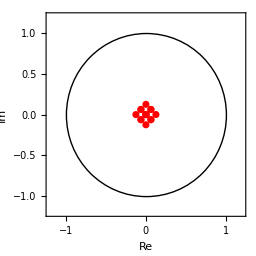
```mathematica
Export["Transform2.pdf",-Graphics--Graphics-];
```

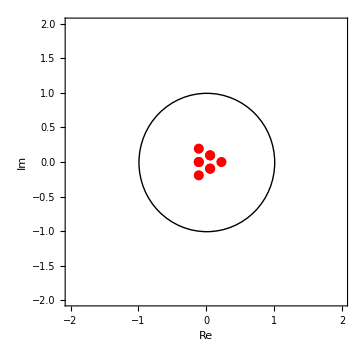
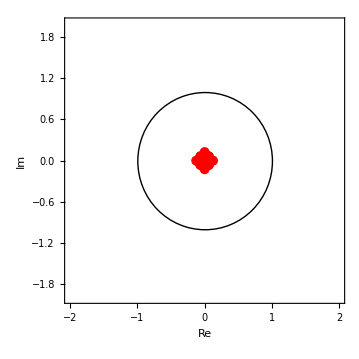
```mathematica
Export["Transform.pdf",-Graphics--Graphics-];
```